```mathematica
N[%]100
```

100 Out[0]

```mathematica
y={.7831,.7739,.6322,.5609,.7497,.8906,.8799,.8745,.7353,.9216,.9175,.9159,.8201,.6916,.682,.6289,.753,.6975}
```

{0.7831,0.7739,0.6322,0.5609,0.7497,0.8906,0.8799,0.8745,0.7353,0.9216,0.9175,0.9159,0.8201,0.6916,0.682,0.6289,0.753,0.6975}

```mathematica
n=Length[y]
```

18

```mathematica
average=Plus@@y/Length[y]
```

0.772678

```mathematica
σ= Sqrt[Plus@@((y-average)^2/(n-1))]
```

0.111093

```mathematica
Δ=N[σ/Sqrt[2n-2]]
```

0.0190523

```mathematica
{σ- Δ,σ+Δ}
```

{0.0920409,0.130146}

```mathematica
PDF[NormalDistribution[average,σ],y]
```

{3.57529,3.59084,1.6144,0.58359,3.51506,2.04436,2.25395,2.35942,3.39345,1.46222,1.53533,1.56427,3.27835,2.75146,2.57366,1.5542,3.53517,2.85616}

```mathematica
Fourier[%9]
```

{10.3806+0. ⅈ,0.708536-0.31436 ⅈ,0.297988-0.656759 ⅈ,1.18023+0.251659 ⅈ,0.704709-0.740454 ⅈ,-0.00220105+1.13531 ⅈ,-0.69749+0.661561 ⅈ,-0.412308+0.227987 ⅈ,-0.152423-0.050757 ⅈ,1.53398+2.39783×10^-17 ⅈ,-0.152423+0.050757 ⅈ,-0.412308-0.227987 ⅈ,-0.69749-0.661561 ⅈ,-0.00220105-1.13531 ⅈ,0.704709+0.740454 ⅈ,1.18023-0.251659 ⅈ,0.297988+0.656759 ⅈ,0.708536+0.31436 ⅈ}

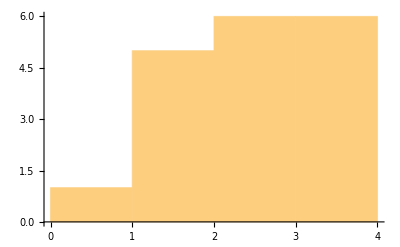

```mathematica
Histogram[%9]
```